## HNL

### Decay width

```mathematica
If[LLPdirName=="HNL",
HNLsList={"HNL-mixing-e","HNL-mixing-mu","HNL-mixing-tau"};
Γtable=Import[FileNameJoin[{dirpheno,LLPdirName,"decay widths","HNLdecayWidth.dat"}],"Table"];
{DecayWidth[mLLP_,U2_,HNLsList[[1]]],DecayWidth[mLLP_,U2_,HNLsList[[2]]],DecayWidth[mLLP_,U2_,HNLsList[[3]]]}=U2(10^Interpolation[{#[[1]],Log10[#[[2]]+10^-99]}&/@Γtable[[All,{1,#}]],InterpolationOrder->1][mLLP])&/@{2,3,4};
ΓLLP[mLLP_,U2_]=If[HNLtype=="Dirac",1/2,1](DecayWidth[mLLP,U2,#]&/@HNLsList).MixingPattern//Chop;
cτLLP[mLLP_,U2_]=chbarval/ΓLLP[mLLP,U2];
]
```

### List of decay processes and sets of decay products for them, branching ratios

#### Mixing e

All processes with at least two charged/neutral particles:

All processes with at least two charged particles:

Processes with jets:

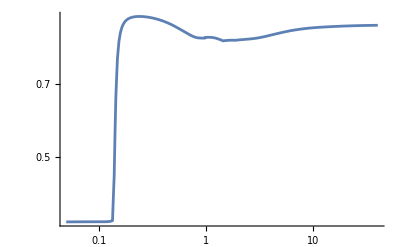

```mathematica
If[LLPdirName=="HNL",
BrRatiosHNLdata[mN_]=Import[FileNameJoin[{dirpheno,LLPdirName,"/decay widths/BrExclusiveMixinge.m"}],"MX"];
LLPsel=HNLsList[[1]];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=Drop[BrRatiosHNLdata[mV][[1]],-1];
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
procsel=ProcessesList[LLPsel,"True"][[i]];
ListBrRatiosTemp[LLPsel,mLLP_,procsel]=BrRatiosHNLdata[mLLP][[3]][[i]];
ListDecayProducts[LLPsel,procsel]=BrRatiosHNLdata[mN][[2]][[i]];
JetsPresence[LLPsel,procsel]=If[MemberQ[{"Jets-qql","Jets-qqv"},procsel],"Yes","No"]
,{i,1,Length[BrRatiosHNLdata[mLLP][[1]]]-1,1}];
Print["All processes with at least two charged/neutral particles:"];
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm;
Do[ListBrRatios[LLPsel,mLLP_,proc]=ListBrRatiosTemp[LLPsel,mLLP,proc]/(Sum[ListBrRatiosTemp[LLPsel,mLLP,pr],{pr,ProcessesList[LLPsel,"True"]}]+BrRatiosHNLdata[mLLP][[3]][[-1]])
,{proc,ProcessesList[LLPsel,"True"]}];
Print["All processes with at least two charged particles:"];
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel];
Print["Processes with jets:"];
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&];
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,40},PlotRange->All]
]
```

```mathematica
ProcessesList[LLPsel,"True"]
```

{π^0ν,ην,2πν,a_1ν,ϕν,ων,η'ν,Jets-qqv,πe,Ke,2πl,Jets-qql,eτν,eμν,eeν,μμν,ττν}

#### Mixing μ

All processes with at least two charged/neutral particles:

All processes with at least two charged particles:

Processes with jets:

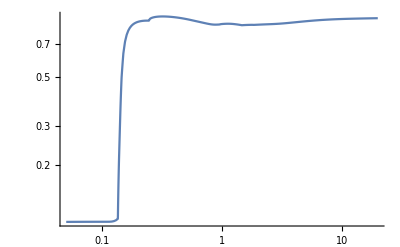

```mathematica
If[LLPdirName=="HNL",
BrRatiosHNLdata[mN_]=Import[FileNameJoin[{dirpheno,LLPdirName,"/decay widths/BrExclusiveMixingμ.m"}],"MX"];
LLPsel=HNLsList[[2]];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=Drop[BrRatiosHNLdata[mN][[1]],-1];
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
procsel=ProcessesList[LLPsel,"True"][[i]];
ListBrRatiosTemp[LLPsel,mLLP_,procsel]=BrRatiosHNLdata[mLLP][[3]][[i]];
ListDecayProducts[LLPsel,procsel]=BrRatiosHNLdata[mN][[2]][[i]];
JetsPresence[LLPsel,procsel]=If[MemberQ[{"Jets-qql","Jets-qqv"},procsel],"Yes","No"]
,{i,1,Length[BrRatiosHNLdata[mLLP][[1]]]-1,1}];
Print["All processes with at least two charged/neutral particles:"];
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm;
Do[ListBrRatios[LLPsel,mLLP_,proc]=ListBrRatiosTemp[LLPsel,mLLP,proc]/(Sum[ListBrRatiosTemp[LLPsel,mLLP,pr],{pr,ProcessesList[LLPsel,"True"]}]+BrRatiosHNLdata[mLLP][[3]][[-1]])
,{proc,ProcessesList[LLPsel,"True"]}];
Print["All processes with at least two charged particles:"];
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel];
Print["Processes with jets:"];
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&];
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,20},PlotRange->All]
]
```

#### Mixing τ

All processes with at least two charged/neutral particles:

All processes with at least two charged particles:

Processes with jets:

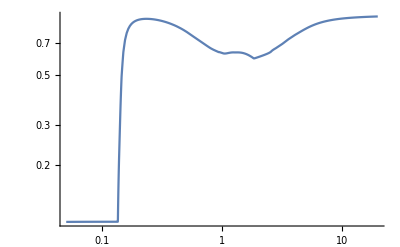

```mathematica
If[LLPdirName=="HNL",
BrRatiosHNLdata[mN_]=Import[FileNameJoin[{dirpheno,LLPdirName,"/decay widths/BrExclusiveMixingτ.m"}],"MX"];
LLPsel=HNLsList[[3]];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=Drop[BrRatiosHNLdata[mV][[1]],-1];
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
procsel=ProcessesList[LLPsel,"True"][[i]];
ListBrRatiosTemp[LLPsel,mLLP_,procsel]=BrRatiosHNLdata[mLLP][[3]][[i]];
ListDecayProducts[LLPsel,procsel]=BrRatiosHNLdata[mN][[2]][[i]];
JetsPresence[LLPsel,procsel]=If[MemberQ[{"Jets-qql","Jets-qqv"},procsel],"Yes","No"]
,{i,1,Length[BrRatiosHNLdata[mLLP][[1]]]-1,1}];
Print["All processes with at least two charged/neutral particles:"];
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm;
Do[ListBrRatios[LLPsel,mLLP_,proc]=ListBrRatiosTemp[LLPsel,mLLP,proc]/(Sum[ListBrRatiosTemp[LLPsel,mLLP,pr],{pr,ProcessesList[LLPsel,"True"]}]+BrRatiosHNLdata[mLLP][[3]][[-1]])
,{proc,ProcessesList[LLPsel,"True"]}];
Print["All processes with at least two charged particles:"];
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel];
Print["Processes with jets:"];
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&];
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,20},PlotRange->All]
]
```

#### Averaging over mixings

```mathematica
If[LLPdirName=="HNL",
(*Channels with the same matrix elements: those not having a lepton produced via charged current*)
SameChannels=Join[Take[ProcessesList["HNL-mixing-e","True"],{1,8}]];
Do[
ListBrRatios["HNL",mLLP_,proc]=DecayWidth[mLLP,1,HNLsList[[1]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[1]],mLLP,proc];
ListDecayProducts[LLPdirName,proc]=ListDecayProducts[HNLsList[[1]],proc];
,{proc,SameChannels}
];
(*Channels with the same final states but different matrix elements*)
ListBrRatios["HNL",mLLP_,"eτν"]=ListBrRatios["HNL",mLLP_,"OverBar[eτν]"]=1/2 DecayWidth[mLLP,MixingPattern[[1]],HNLsList[[1]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[1]],mLLP,"eτν"]+1/2 DecayWidth[mLLP,MixingPattern[[3]],HNLsList[[3]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[3]],mLLP,"τeν"];
ListDecayProducts[LLPdirName,"eτν"]=ListDecayProducts[HNLsList[[1]],"eτν"];
ListDecayProducts[LLPdirName,"OverBar[eτν]"]={"e^+","τ^-","(ν̄)_τ","Null"};
ListBrRatios["HNL",mLLP_,"eμν"]=ListBrRatios["HNL",mLLP_,"OverBar[eμν]"]=1/2 DecayWidth[mLLP,MixingPattern[[1]],HNLsList[[1]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[1]],mLLP,"eμν"]+1/2 DecayWidth[mLLP,MixingPattern[[2]],HNLsList[[2]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[2]],mLLP,"μeν"];
ListDecayProducts[LLPdirName,"eμν"]=ListDecayProducts[HNLsList[[1]],"eμν"];
ListDecayProducts[LLPdirName,"OverBar[eμν]"]={"e^+","μ^-","(ν̄)_μ","Null"};
ListBrRatios["HNL",mLLP_,"μτν"]=ListBrRatios["HNL",mLLP_,"OverBar[μτν]"]=1/2 DecayWidth[mLLP,MixingPattern[[2]],HNLsList[[2]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[2]],mLLP,"μτν"]+1/2 DecayWidth[mLLP,MixingPattern[[3]],HNLsList[[3]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[3]],mLLP,"τμν"];
ListDecayProducts[LLPdirName,"μτν"]=ListDecayProducts[HNLsList[[2]],"μτν"];
ListDecayProducts[LLPdirName,"OverBar[μτν]"]={"μ^+","τ^-","(ν̄)_τ","Null"};
(*Channels with the same final states but different matrix elements and hence br ratios - N -> llν*)
Do[
ListBrRatios[LLPdirName,mLLP_,proc]=Sum[DecayWidth[mLLP,MixingPattern[[i]],HNLsList[[i]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[i]],mLLP,proc],{i,1,3,1}];
ListDecayProducts[LLPdirName,proc]=ListDecayProducts[HNLsList[[1]],proc];
,{proc,{"eeν","μμν","ττν"}}];
(*Channels with different final states*)
ListBrRatios[LLPdirName,mLLP_,"Jets-qqe"]=ListBrRatios[LLPdirName,mLLP_,"OverBar[Jets - qqe]"]=1/2 DecayWidth[mLLP,MixingPattern[[1]],HNLsList[[1]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[1]],mLLP,"Jets-qql"];
ListDecayProducts[LLPdirName,"Jets-qqe"]={"u","d̄","e^-","Null"};
ListDecayProducts[LLPdirName,"OverBar[Jets - qqe]"]={"ū","d","e^+","Null"};
ListBrRatios[LLPdirName,mLLP_,"Jets-qqμ"]=ListBrRatios[LLPdirName,mLLP_,"OverBar[Jets - qqμ]"]=1/2 DecayWidth[mLLP,MixingPattern[[2]],HNLsList[[2]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[2]],mLLP,"Jets-qql"];
ListDecayProducts[LLPdirName,"Jets-qqμ"]={"u","d̄","μ^-","Null"};
ListDecayProducts[LLPdirName,"OverBar[Jets - qqμ]"]={"ū","d","μ^+","Null"};
ListBrRatios[LLPdirName,mLLP_,"Jets-qqτ"]=ListBrRatios[LLPdirName,mLLP_,"OverBar[Jets - qqτ]"]=1/2 DecayWidth[mLLP,MixingPattern[[3]],HNLsList[[3]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[3]],mLLP,"Jets-qql"];
ListDecayProducts[LLPdirName,"Jets-qqτ"]={"u","d̄","τ^-","Null"};
ListDecayProducts[LLPdirName,"OverBar[Jets - qqτ]"]={"ū","d","τ^+","Null"};
ListBrRatios["HNL",mLLP_,"Ke"]=ListBrRatios["HNL",mLLP_,"OverBar[Ke]"]=1/2 DecayWidth[mLLP,MixingPattern[[1]],HNLsList[[1]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[1]],mLLP,"Ke"];
ListDecayProducts[LLPdirName,"Ke"]={"K^+","e^-","Null","Null"};
ListDecayProducts[LLPdirName,"OverBar[Ke]"]={"K^-","e^+","Null","Null"};
ListBrRatios["HNL",mLLP_,"Kμ"]=ListBrRatios["HNL",mLLP_,"OverBar[Kμ]"]=1/2 DecayWidth[mLLP,MixingPattern[[2]],HNLsList[[2]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[2]],mLLP,"Kμ"];
ListDecayProducts[LLPdirName,"Kμ"]={"K^+","μ^-","Null","Null"};
ListDecayProducts[LLPdirName,"OverBar[Kμ]"]={"K^-","μ^+","Null","Null"};
ListBrRatios["HNL",mLLP_,"Kτ"]=ListBrRatios["HNL",mLLP_,"OverBar[Kτ]"]=1/2 DecayWidth[mLLP,MixingPattern[[3]],HNLsList[[3]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[3]],mLLP,"Kτ"];
ListDecayProducts[LLPdirName,"Kτ"]={"K^+","τ^-","Null","Null"};
ListDecayProducts[LLPdirName,"OverBar[Kτ]"]={"K^-","τ^+","Null","Null"};
ListBrRatios["HNL",mLLP_,"2πe"]=ListBrRatios["HNL",mLLP_,"OverBar[2  πe]"]=1/2 DecayWidth[mLLP,MixingPattern[[1]],HNLsList[[1]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[1]],mLLP,"2πl"];
ListDecayProducts[LLPdirName,"2πe"]=ListDecayProducts[HNLsList[[1]],"2πl"];
ListDecayProducts[LLPdirName,"OverBar[2  πe]"]={"π^-","π^0","e^+","Null"};
ListBrRatios["HNL",mLLP_,"2πμ"]=ListBrRatios["HNL",mLLP_,"OverBar[2  πμ]"]=1/2 DecayWidth[mLLP,MixingPattern[[2]],HNLsList[[2]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[2]],mLLP,"2πl"];
ListDecayProducts[LLPdirName,"2πμ"]=ListDecayProducts[HNLsList[[2]],"2πl"];
ListDecayProducts[LLPdirName,"OverBar[2  πμ]"]={"π^-","π^0","μ^+","Null"};
ListBrRatios["HNL",mLLP_,"2πτ"]=ListBrRatios["HNL",mLLP_,"OverBar[2  πτ]"]=1/2 DecayWidth[mLLP,MixingPattern[[3]],HNLsList[[3]]]/ΓLLP[mLLP,1] ListBrRatios[HNLsList[[3]],mLLP,"2πl"];
ListDecayProducts[LLPdirName,"2πτ"]=ListDecayProducts[HNLsList[[3]],"2πl"];
ListDecayProducts[LLPdirName,"OverBar[2  πτ]"]={"π^-","π^0","τ^+","Null"};
]
```

```mathematica
ListBrRatios[HNLsList[[1]],mLLP,"2πl","Default"]
```

ListBrRatios(HNL-mixing-e,mLLP,2πe,Default)

```mathematica
Select[Keys[DownValues@ListBrRatios][[All,1,#]]&/@Range[1,4]//Transpose,#[[1]]==HNLsList[[1]]&]
```

(HNL-mixing-e | mLLP$_ | 2ev | Default
HNL-mixing-e | mLLP$_ | 2muv | Default
HNL-mixing-e | mLLP$_ | 2Pie | Default
HNL-mixing-e | mLLP$_ | 2Piv | Default
HNL-mixing-e | mLLP$_ | 2tauv | Default
HNL-mixing-e | mLLP$_ | a1v | Default
HNL-mixing-e | mLLP$_ | emuv | Default
HNL-mixing-e | mLLP$_ | EtaPrv | Default
HNL-mixing-e | mLLP$_ | etauv | Default
HNL-mixing-e | mLLP$_ | Etav | Default
HNL-mixing-e | mLLP$_ | Jets-ccv | Default
HNL-mixing-e | mLLP$_ | Jets-cse | Default
HNL-mixing-e | mLLP$_ | Jets-ddv | Default
HNL-mixing-e | mLLP$_ | Jets-ssv | Default
HNL-mixing-e | mLLP$_ | Jets-ude | Default
HNL-mixing-e | mLLP$_ | Jets-uuv | Default
HNL-mixing-e | mLLP$_ | Ke | Default
HNL-mixing-e | mLLP$_ | Omegav | Default
HNL-mixing-e | mLLP$_ | Phiv | Default
HNL-mixing-e | mLLP$_ | Pi0v | Default
HNL-mixing-e | mLLP$_ | Pie | Default)

### Matrix elements

#### N->ππν/ππl

```mathematica
If[LLPdirName=="HNL",
MNtolππ=1/(√2)SpinorUBar[p3,m3].GA[μ].(1-GA[5]).SpinorU[p,m]*((-MT[μ,ν]+(FV[p-p3,μ]*FV[p-p3,ν])/mρ^2)/(√((ExpandScalarProduct[ScalarProduct[p-p3,p-p3]]-mρ^2)^2+Γρ^2*mρ^2)))*(FV[p2-p1,ν])//Contract//ExpandScalarProduct;
MNtolππStar=ComplexConjugate[MNtolππ];
MNtolππSquaredTemp=1/2 FermionSpinSum[MNtolππ*MNtolππStar]/.DiracTrace->TR//Contract//Simplify//ExpandScalarProduct;
MNtolππSquaredTemp2[E1_,E3_,m_,m1_,m2_,m3_]=(MNtolππSquaredTemp/.{ScalarProduct[p,p1]->ProductKK1energy,ScalarProduct[p,p2]->ProductKK2energy,ScalarProduct[p1,p2]->ProductK1K2energy,ScalarProduct[p,p]->ProductKK,ScalarProduct[p,p3]->ProductKK3energy,ScalarProduct[p2,p2]->ProductK2K2,ScalarProduct[p3,p3]->ProductK3K3,ScalarProduct[p2,p3]->ProductK2K3energy,ScalarProduct[p1,p3]->ProductK1K3energy,ScalarProduct[p1,p1]->ProductK1K1}//Expand//Simplify)/.{Γρ->0.1478,mρ->ParamProductMass[113.]};
Do[
fip=LLP;
proc=PROC;
mprodlist=ParamProductMass[#]&/@(ParamProductToPDGid[#]&/@ListDecayProducts[fip,proc]);
Msquared3BodyLLP[fip,proc,E1_,E3_,mLLP_]=MNtolππSquaredTemp2[E1,E3,mLLP,m1,m2,m3]/.Table[Symbol["m"<>ToString[i]]->mprodlist[[i]],{i,1,3,1}]//Simplify
,{PROC,{"2πl","2πν"}},{LLP,HNLsList}]
]
```

#### N→ q+q̄'+l, q+q̄+ν

```mathematica
If[LLPdirName=="HNL",
(*____________________________________________________*)
(*qql*)
(*____________________________________________________*)
M3bodyqql=1/(2 √2)SpinorUBar[k3,m3].GA[μ].(1-GA5).SpinorU[k,m]*SpinorUBar[k1,m1].GA[μ].(1-GA5).SpinorV[k2,m2]//Contract;
M3bodyqqlStar=ComplexConjugate[M3bodyqql];
M3bodyqqlSquared[E1_,E3_,m_,m1_,m2_,m3_]=Simplify[Expand[FermionSpinSum[M3bodyqql M3bodyqqlStar]/.DiracTrace->TR//Contract//Simplify]]/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k2,k2]->ProductK2K2,ScalarProduct[k,k2]->ProductKK2energy,ScalarProduct[k,k1]-> ProductKK1energy,ScalarProduct[k,k3]->ProductKK3energy,ScalarProduct[k1,k3]->ProductK1K3energy ,ScalarProduct[k1,k2]->ProductK1K2energy,ScalarProduct[k2,k3]-> ProductK2K3energy}//Simplify;
Do[
fip=LLP;
proc="Jets-qql";
mprodlist=ParamProductMass[#]&/@(ParamProductToPDGid[#]&/@ListDecayProducts[fip,proc]);
Msquared3BodyLLP[fip,proc,E1_,E3_,mLLP_]=M3bodyqqlSquared[E1,E3,mLLP,m1,m2,m3]/.Table[Symbol["m"<>ToString[i]]->mprodlist[[i]],{i,1,3,1}]//Chop//Simplify
,{LLP,HNLsList}];
(*____________________________________________________*)
(*qqν, assuming that the main contribution comes from u/d quarks*)
(*____________________________________________________*)
M3bodyqqν=1/2*1/(4 √2)(SpinorUBar[k3,m3].GA[μ].(1-GA5).SpinorU[k,m]*SpinorUBar[k1,m1].GA[μ].(1-4/3 sin2θw-GA5).SpinorV[k2,m2]+SpinorUBar[k3,m3].GA[μ].(1-GA5).SpinorU[k,m]*SpinorUBar[k1,m1].GA[μ].(1+8/3 sin2θw-GA5).SpinorV[k2,m2])//Contract;
M3bodyqqνStar=ComplexConjugate[M3bodyqqν];
M3bodyqqνSquared[E1_,E3_,m_,m1_,m2_,m3_]=Simplify[Expand[FermionSpinSum[M3bodyqqν M3bodyqqνStar]/.DiracTrace->TR//Contract//Simplify]]/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k2,k2]->ProductK2K2,ScalarProduct[k,k2]->ProductKK2energy,ScalarProduct[k,k1]-> ProductKK1energy,ScalarProduct[k,k3]->ProductKK3energy,ScalarProduct[k1,k3]->ProductK1K3energy ,ScalarProduct[k1,k2]->ProductK1K2energy,ScalarProduct[k2,k3]-> ProductK2K3energy}//Simplify;
Do[
fip=LLP;
proc="Jets-qqv";
mprodlist=ParamProductMass[#]&/@(ParamProductToPDGid[#]&/@ListDecayProducts[fip,proc]);
Msquared3BodyLLP[fip,proc,E1_,E3_,mLLP_]=M3bodyqqνSquared[E1,E3,mLLP,m1,m2,m3]/.Table[Symbol["m"<>ToString[i]]->mprodlist[[i]],{i,1,3,1}]/.{sin2θw->0.23}//Chop//Simplify
,{LLP,HNLsList}]
]
```

#### N->l+l'+ν

```mathematica
If[LLPdirName=="HNL",
procsleptonic[HNLsList[[3]]]={"τeν","τμν","eeν","μμν","ττν"};
procsleptonic[HNLsList[[2]]]={"μeν","μτν","eeν","μμν","ττν"};
procsleptonic[HNLsList[[1]]]={"eμν","eτν","eeν","μμν","ττν"};
(*________________________________*)
(*l != l'*)
(*________________________________*)
M3bodyllprν=1/(2 √2)SpinorUBar[k1,m1].GA[μ].(1-GA5).SpinorU[k,m]*SpinorUBar[k2,m2].GA[μ].(1-GA5).SpinorV[k3,m3]//Contract;
M3bodyllprνStar=ComplexConjugate[M3bodyllprν];
M3bodyllprνSquared[E1_,E3_,m_,m1_,m2_,m3_]=Simplify[Expand[FermionSpinSum[M3bodyllprν M3bodyllprνStar]/.DiracTrace->TR//Contract//Simplify]]/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k2,k2]->ProductK2K2,ScalarProduct[k,k2]->ProductKK2energy,ScalarProduct[k,k1]-> ProductKK1energy,ScalarProduct[k,k3]->ProductKK3energy,ScalarProduct[k1,k3]->ProductK1K3energy ,ScalarProduct[k1,k2]->ProductK1K2energy,ScalarProduct[k2,k3]-> ProductK2K3energy}//Simplify;
Do[
fip=LLP;
Do[
mprodlist=ParamProductMass[#]&/@(ParamProductToPDGid[#]&/@ListDecayProducts[LLP,proc]);
Msquared3BodyLLP[LLP,proc,E1_,E3_,mLLP_]=M3bodyllprνSquared[E1,E3,mLLP,m1,m2,m3]/.Table[Symbol["m"<>ToString[i]]->mprodlist[[i]],{i,1,3,1}]//Chop//Simplify
,{proc,Drop[procsleptonic[fip],-3]}]
,{LLP,HNLsList}];
(*________________________________*)
(*l = l'. Two contributions - from charged and from neutral currents*)
(*________________________________*)
M3bodyllν=(1/(2 √2)SpinorUBar[k1,m1].GA[μ].(1-GA5).SpinorU[k,m]*SpinorUBar[k3,m3].GA[μ].(1-GA5).SpinorV[k2,m2]//Contract)+(1/(4 √2)SpinorUBar[k3,m3].GA[μ].(1-GA5).SpinorU[k,m]*SpinorUBar[k1,m1].GA[μ].(1-4sin2θw-GA5).SpinorV[k2,m2]//Contract);
M3bodyllνStar=ComplexConjugate[M3bodyllν];
M3bodyllνSquared[E1_,E3_,m_,m1_,m2_,m3_]=1/2 Simplify[Expand[FermionSpinSum[M3bodyllν M3bodyllνStar]/.DiracTrace->TR//Contract//Simplify]]/.{ScalarProduct[k,k]->ProductKK,ScalarProduct[k2,k2]->ProductK2K2,ScalarProduct[k,k2]->ProductKK2energy,ScalarProduct[k,k1]-> ProductKK1energy,ScalarProduct[k,k3]->ProductKK3energy,ScalarProduct[k1,k3]->ProductK1K3energy ,ScalarProduct[k1,k2]->ProductK1K2energy,ScalarProduct[k2,k3]-> ProductK2K3energy}//Simplify;
Do[
fip=LLP;
Do[
mprodlist=ParamProductMass[#]&/@(ParamProductToPDGid[#]&/@ListDecayProducts[fip,proc]);
Msquared3BodyLLP[LLP,proc,E1_,E3_, mLLP_]=M3bodyllνSquared[E1,E3,mLLP,m1,m2,m3]/.Table[Symbol["m"<>ToString[i]]->mprodlist[[i]],{i,1,3,1}]/.{sin2θw->0.23}//Chop//Simplify
,{proc,Drop[procsleptonic[fip],2]}]
,{LLP,HNLsList}]
]
```

#### Averaging over mixings

```mathematica
If[LLPdirName=="HNL",
(*For processes unique for each mixing/with the same matrix element*)
Msquared3BodyLLP[LLPdirName,"2πe",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[2  πe]",E1_,E3_, mLLP_]=Msquared3BodyLLP[HNLsList[[1]],"2πl",E1,E3, mLLP];
Msquared3BodyLLP[LLPdirName,"2πμ",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[2  πμ]",E1_,E3_, mLLP_]=Msquared3BodyLLP[HNLsList[[2]],"2πl",E1,E3, mLLP];
Msquared3BodyLLP[LLPdirName,"2πτ",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[2  πτ]",E1_,E3_, mLLP_]=Msquared3BodyLLP[HNLsList[[3]],"2πl",E1,E3, mLLP];
Msquared3BodyLLP[LLPdirName,"2πν",E1_,E3_, mLLP_]=Msquared3BodyLLP[HNLsList[[1]],"2πν",E1,E3, mLLP];
Msquared3BodyLLP[LLPdirName,"Jets-qqe",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[Jets - qqe]",E1_,E3_, mLLP_]=Msquared3BodyLLP[HNLsList[[1]],"Jets-qql",E1,E3, mLLP];
Msquared3BodyLLP[LLPdirName,"Jets-qqμ",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[Jets - qqμ]",E1_,E3_, mLLP_]=Msquared3BodyLLP[HNLsList[[2]],"Jets-qql",E1,E3, mLLP];
Msquared3BodyLLP[LLPdirName,"Jets-qqτ",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[Jets - qqτ]",E1_,E3_, mLLP_]=Msquared3BodyLLP[HNLsList[[3]],"Jets-qql",E1,E3, mLLP];
Msquared3BodyLLP[LLPdirName,"Jets-qqv",E1_,E3_, mLLP_]=Msquared3BodyLLP[HNLsList[[1]],"Jets-qqv",E1,E3, mLLP];
(*For the processes N -> llν*)
Msquared3BodyLLP[LLPdirName,"eμν",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[eμν]",E1_,E3_, mLLP_]=DecayWidth[mLLP,MixingPattern[[1]],HNLsList[[1]]]/ΓLLP[mLLP,1] Msquared3BodyLLP[HNLsList[[1]],"eμν",E1,E3, mLLP]+DecayWidth[mLLP,MixingPattern[[2]],HNLsList[[2]]]/ΓLLP[mLLP,1] Msquared3BodyLLP[HNLsList[[2]],"μeν",E1,E3, mLLP]//Simplify;
Msquared3BodyLLP[LLPdirName,"eτν",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[eτν]",E1_,E3_, mLLP_]=DecayWidth[mLLP,MixingPattern[[1]],HNLsList[[1]]]/ΓLLP[mLLP,1] Msquared3BodyLLP[HNLsList[[1]],"eτν",E1,E3, mLLP]+DecayWidth[mLLP,MixingPattern[[3]],HNLsList[[3]]]/ΓLLP[mLLP,1] Msquared3BodyLLP[HNLsList[[3]],"τeν",E1,E3, mLLP]//Simplify;
Msquared3BodyLLP[LLPdirName,"μτν",E1_,E3_, mLLP_]=Msquared3BodyLLP[LLPdirName,"OverBar[μτν]",E1_,E3_, mLLP_]=DecayWidth[mLLP,MixingPattern[[2]],HNLsList[[2]]]/ΓLLP[mLLP,1] Msquared3BodyLLP[HNLsList[[2]],"μτν",E1,E3, mLLP]+DecayWidth[mLLP,MixingPattern[[3]],HNLsList[[3]]]/ΓLLP[mLLP,1] Msquared3BodyLLP[HNLsList[[3]],"τμν",E1,E3, mLLP]//Simplify;
Do[
Msquared3BodyLLP[LLPdirName,proc,E1_,E3_, mLLP_]=Sum[DecayWidth[mLLP,MixingPattern[[i]],HNLsList[[i]]]/ΓLLP[mLLP,1] Msquared3BodyLLP[HNLsList[[i]],proc,E1,E3, mLLP],{i,1,3,1}]//Simplify
,{proc,{"eeν","μμν","ττν"}}]
]
```

```mathematica
(*Table[{proc,Msquared3BodyLLP[LLPdirName,proc,E1,E3, 1.5]},{proc,ListDecaysLLPselected}]*)
```

(π^0ν | Msquared3BodyLLP(HNL,π^0ν,E1,E3,1.5)
ην | Msquared3BodyLLP(HNL,ην,E1,E3,1.5)
2πν | (8.316 (4.329 E1^2+(4.329 E1-2.46335) E3-6.49351 E1+2.43507))/(9. E3^2-9.89625 E3+2.73356)
a_1ν | Msquared3BodyLLP(HNL,a_1ν,E1,E3,1.5)
ϕν | Msquared3BodyLLP(HNL,ϕν,E1,E3,1.5)
ων | Msquared3BodyLLP(HNL,ων,E1,E3,1.5)
η'ν | Msquared3BodyLLP(HNL,η'ν,E1,E3,1.5)
Jets-qqv | 1.5 (0.0352667 E1 (1.5-2 E1)-6.95527 (E1+E3-1.5) (2 E1+2 E3-1.5)+0.012035 E3)
OverBar[eτν] | 0.-48. E3 (1.5 E3+0.44145)
eτν | 0.-48. E3 (1.5 E3+0.44145)
OverBar[eμν] | 0.-48. E3 (1.5 E3-1.11949)
eμν | 0.-48. E3 (1.5 E3-1.11949)
OverBar[μτν] | 0.
μτν | 0.
eeν | 3. (-3.1974 (E1+E3-1.5) (2 E1+2 E3-1.5)-0.3174 E1 (2 E1-1.5)+3.358×10^-7 E3)+0.
μμν | 3. (-3.1974 (E1+E3-1.5) (2 E1+2 E3-1.5)-0.3174 E1 (2 E1-1.5)+0.0148088 E3)+0.
ττν | 3. (-3.1974 (E1+E3-1.5) (2 E1+2 E3-1.5)-0.3174 E1 (2 E1-1.5)+4.20811 E3)+0.
OverBar[Jets - qqe] | -24. (-3. E1-3. E3+2.25) (-1. E1-1. E3+1.5)
Jets-qqe | -24. (-3. E1-3. E3+2.25) (-1. E1-1. E3+1.5)
OverBar[Jets - qqμ] | -24. (-3. E1-3. E3+2.26103) (-1. E1-1. E3+1.5)
Jets-qqμ | -24. (-3. E1-3. E3+2.26103) (-1. E1-1. E3+1.5)
OverBar[Jets - qqτ] | -24. (-3. E1-3. E3+5.3829) (-1. E1-1. E3+1.5)
Jets-qqτ | -24. (-3. E1-3. E3+5.3829) (-1. E1-1. E3+1.5)
OverBar[Ke] | Msquared3BodyLLP(HNL,OverBar[Ke],E1,E3,1.5)
Ke | Msquared3BodyLLP(HNL,Ke,E1,E3,1.5)
OverBar[Kμ] | Msquared3BodyLLP(HNL,OverBar[Kμ],E1,E3,1.5)
Kμ | Msquared3BodyLLP(HNL,Kμ,E1,E3,1.5)
OverBar[Kτ] | Msquared3BodyLLP(HNL,OverBar[Kτ],E1,E3,1.5)
Kτ | Msquared3BodyLLP(HNL,Kτ,E1,E3,1.5)
OverBar[2  πe] | (8.316 (2 (0.900938 (1.5-2. E1)+0.000825859) (0.903-1.20125 E1)+(4.329 E1-2.46706) E3))/(9. E3^2-9.89625 E3+2.73356)
2πe | (8.316 (2 (0.900938 (1.5-2. E1)+0.000825859) (0.903-1.20125 E1)+(4.329 E1-2.46706) E3))/(9. E3^2-9.89625 E3+2.73356)
OverBar[2  πμ] | (8.316 (2 (0.900938 (1.5-2. E1)+0.0008107) (0.903-1.20125 E1)+(4.329 E1-2.46306) E3))/(9. E3^2-9.9624 E3+2.77005)
2πμ | (8.316 (2 (0.900938 (1.5-2. E1)+0.0008107) (0.903-1.20125 E1)+(4.329 E1-2.46306) E3))/(9. E3^2-9.9624 E3+2.77005)
OverBar[2  πτ] | (8.316 (2 (0.900938 (1.5-2. E1)-0.00348188) (0.903-1.20125 E1)+(4.329 E1-1.33168) E3))/(9. E3^2-28.6937 E3+22.8833)
2πτ | (8.316 (2 (0.900938 (1.5-2. E1)-0.00348188) (0.903-1.20125 E1)+(4.329 E1-1.33168) E3))/(9. E3^2-28.6937 E3+22.8833))